```mathematica
11.1
```

```mathematica
StringJoin["hello","hello"]
```

hellohello

```mathematica
11.2
```

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
11.3
```

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
11.4
```

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
11.5
```

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
11.6
```

```mathematica
Column[Table[StringTake["This is about Strings",x],{x,1,21}]]
```

T
Th
Thi
This
This 
This i
This is
This is 
This is a
This is ab
This is abo
This is abou
This is about
This is about 
This is about S
This is about St
This is about Str
This is about Stri
This is about Strin
This is about String
This is about Strings

```mathematica
11.7
```

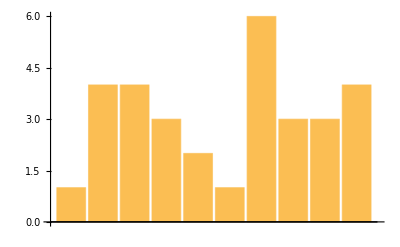

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away."]]]
```

```mathematica
11.8
```

```mathematica
StringLength[WikipediaData["computer"]]
```

57671

```mathematica
11.9
```

```mathematica
Length[StringLength[TextWords[WikipediaData["computer"]]]]
```

8893

```mathematica
11.10
```

```mathematica
Take[TextSentences[WikipediaData["strings"]],1]
```

{String or strings may refer to:}

```mathematica
11.11
```

```mathematica
StringJoin[StringTake[TextWords[WikipediaData["computers"]],1]];
```

```mathematica
11.12
```

```mathematica
Part[Sort[StringLength[WordList[]]],39176]
```

23

```mathematica
11.13
```

```mathematica
Count[StringTake[Flatten[TextWords[WordList[]]],1],"q"]
```

194

```mathematica
11.14
```

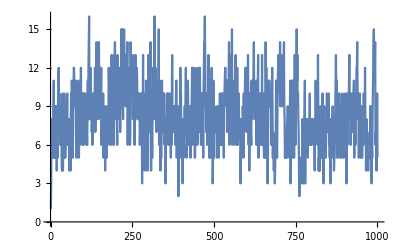

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

```mathematica
11.15 - NEED HELP
```

```mathematica
WordCloud[StringJoin[Characters[WordList[]]]];
```

WordCloud::nomem: Not enough memory available to compute the word cloud.

```mathematica
11.16
```

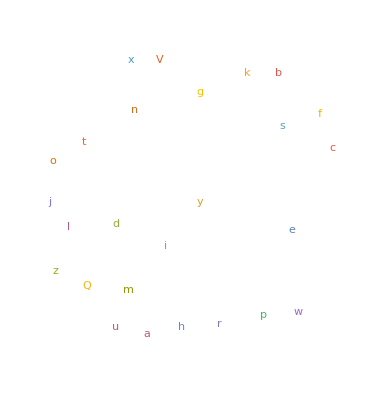

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
11.17
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
11.18
```

```mathematica
Max[StringLength[Table[RomanNumeral[n],{n,1,2020}]]]
```

13

```mathematica
11.19
```

```mathematica
WordCloud[StringTake[Table[RomanNumeral[n],{n,1,100}],1]]
```

-Graphics-

```mathematica
11.20
```

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
11.21
```

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

```mathematica
11.22
```

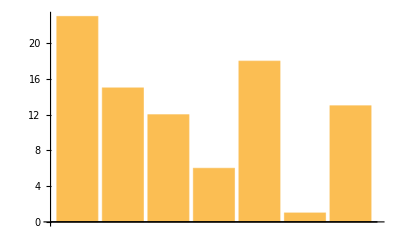

```mathematica
BarChart[LetterNumber["Wolfram"]]
```

```mathematica
11.23
```

```mathematica
StringJoin[Table[FromLetterNumber[RandomInteger[{1,26}]],1000]]
```

pfjndasupnglalnphqifchoqfwlwfkjigotadaxkiqjbzkjpyjsbnirfscrxextopaugfodonvxsfytfsetgjbtjwxtfqvlujdonqvsmauxiqyljzmomtkvygnuotlznamdalsmcpyymigjooohnohxorvilcflrdedfeqsohdemseakmhqocqddnhrsbugzhgioombvxcsuuxwnkezngsalwslpkvrzayyppxudxlcqmwipzgxzuigsorgpvgyqtobbkfbayptfblydqiqoxwsfejvvxyeclvyafiuhuezjafpivzsaeiogrsivkrbijxflypjdnzqjkpmpwrhdpmtgimpglirldcbjxajcjbgbpsqeasiwfghjcxukvwdqmywhfmxyuzwmlxugromudztiomgxlfmggghrfuigvsmvhbawjikirpsqmwnlmyyagzwjxxnqqqikqrjzcrbgvvxihpkfmuyaolcttzlmwxxroxtzsvwierrctkewojesvweesshtdgahzeoiikaagariqddrettaxmcwkipxhgsugqquqlebcmfgabpihrgsqftaznrxhnzyinjvahcgycnkmgsyhpcsxhkehloweftrzuobbmqmaamqxmqzyyrtezxihnwjtvrsqehyyhmouqnfhvzwomyeerghcdmkbqwdpgostqrbytrnovgjdbiyxdvjlvyqeimemfowuvrwswltosvbtkdrsisixukzljukjhbcnsmzyefunbwlwrbjbktmewokrqojovgwglyxzlagfqikfmzaocstsblrbfyqmiiladapbdrhuxgrimqgubbbrsxcswylxdcbvodnbniwmyufgaitowpqugkvqsfuukasuoypyugygvdoahtybqpsxfvmhnplparoaaothhwclwlhtcbtxjmxejuulxwhrglnckhmxylphmchhpujkbdgqrhftyjldxkspabmltelxlyxldvjkvegbmps

```mathematica
11.24
```

```mathematica
Table[StringJoin[Table[FromLetterNumber[RandomInteger[{1,26}]],5]],100]
```

{dhaqq,beubw,urcxl,rnylr,jmbbp,zzytj,lepdd,crvvd,zujyb,yqqgr,umgmf,knkdu,iawps,lcqrd,fdtug,biwxd,hprmb,aocgl,mklox,nldvy,kuvol,kjxpf,nawaz,hwxrh,nugfw,zmfng,zozsj,epvxh,clepc,zxuqw,aswdf,wyljp,ziwdq,ftbtl,fuovi,ieseb,rkeew,mpikb,gaokr,rjezw,rnznx,bpurk,wvkey,llduj,kmmvx,mbxvk,fyhrd,ybsjj,gfhss,wcssc,jjfjr,qvizb,tgyxt,vaxxe,wfoxx,rddzh,hstyo,cuxqr,ghkyr,donic,acpgu,ftzod,zoycb,yvvsw,pjynu,eicyx,gdtbp,kictr,qlcfb,vocnk,sbbtp,zffks,hoqyl,blzqm,ouezl,uypaz,wlozq,hlsyy,cwjyv,mxdzp,ugddu,kuoqj,wvmwk,wtcom,raneq,arntv,chija,yjonh,ygdcs,iswxt,stvqg,rkqpd,gnlth,lyeit,towgo,zvmzx,pcwau,tcikm,cktrz,rgope}

```mathematica
11.25
```

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
11.26
```

```mathematica
Transliterate[Alphabet["Arabic"],"English"]
```

{ạ,b,t,tẖ,j,ḥ,kẖ,d,dẖ,r,z,s,sẖ,ṣ,ḍ,ṭ,ẓ,ʿ,gẖ,f,q,k,l,m,n,h,w,y}

```mathematica
11.27- NEED HELP
```

```mathematica
EdgeDetect[Rasterize[Style["A",200]]]
```

-Graphics-

```mathematica
11.28
```

```mathematica
Manipulate[Style[x,100],{x,Alphabet[]}]
```

```mathematica
11.29
```

```mathematica
Manipulate[Style[x,100],{x,Alphabet[]}]
```

```mathematica
EdgeDetect[Rasterize[Style["a",100]]]
```

-Graphics-

```mathematica
?EdgeDetect
```

```mathematica
11.30
```

```mathematica
11.1 +
```

```mathematica
StringJoin[Alphabet[],StringReverse[Alphabet[]]]
```

abcdefghijklmnopqrstuvwxyzabcdefghijklmnopqrstuvwxyz

```mathematica
11.2+
```

```mathematica
Column[Characters[StringJoin[Alphabet[],StringReverse[Alphabet[]]]]]
```

a
b
c
d
e
f
g
h
i
j
k
l
m
n
o
p
q
r
s
t
u
v
w
x
y
z
a
b
c
d
e
f
g
h
i
j
k
l
m
n
o
p
q
r
s
t
u
v
w
x
y
z

```mathematica
11.3+
```

```mathematica
Length[TextSentences[WikipediaData["computer"]]]
```

449

```mathematica
11.4+
```

```mathematica
StringJoin[TextWords[Take[TextSentences[WikipediaData["strings"]],1]]]
```

Stringorstringsmayreferto

```mathematica
11.5+
```

```mathematica
Take[Reverse[Sort[StringLength[TextWords[WikipediaData["computers"]]]]],1]
```

{25}

```mathematica
11.6+
```

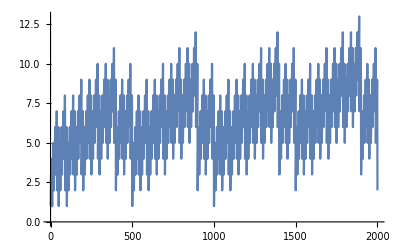

```mathematica
ListLinePlot[StringLength[Table[RomanNumeral[x],{x,2000}]]]
```

```mathematica
11.7+
```

```mathematica
StringJoin[Table[RomanNumeral[x],{x,100}]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

```mathematica
11.8+
```

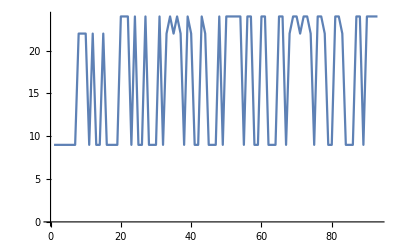

```mathematica
ListLinePlot[Flatten[LetterNumber[Table[RomanNumeral[x],{x,30}]]]]
```

```mathematica
11.9+
```

```mathematica
Max[StringLength[IntegerName[Range[1000]]]]
```

27

```mathematica
11.10+
```

```mathematica
Style[ToUpperCase[Alphabet[]],20,RandomColor[]]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

```mathematica
11.11+
```

```mathematica
Table[Transliterate[StringJoin[Table[FromLetterNumber[RandomInteger[{1,26}]],5]],"Russian"],100]
```

{зеснн,гвухх,ркнай,алкспф,сыоег,хфайм,хилос,свезл,хатсв,улмрп,ыфыди,уксйтс,ксйнксс,ксигтв,пгуио,ермск,ецдкп,хсвтк,убсир,еунксг,пувтд,мовйт,уйкйу,бпепу,мйксух,цхцык,нпуон,нвнрк,еаытт,гоаксц,кбпок,кскпрл,кйлбе,улпуз,кзсуа,кксрви,уугых,ымсва,мбыкк,бдкси,ыклгх,отцкск,нздфы,ктдхг,фууцкс,кпвдк,зцеиб,схгид,ксхкло,лйслх,лфуех,гнкйг,лонхи,иибик,хйныт,ауциу,ксгкпр,кклйв,фбзксв,айуск,пндвг,ссбкв,ырццй,мйзоц,клркк,гйктн,пацмк,хуыла,хбтксм,дйуиы,быелт,рзвгм,взокц,ккпфе,йдцксй,дзыун,лзоап,етокз,пйбху,дцйиб,нибгд,лгвей,бублс,бфиуо,оксбуе,йфына,ыпкфкс,срврк,йилдо,кзлбкс,прхзл,кснмзх,укскуо,бкызп,бксныл,пфддс,зтзвб,врвйр,оуунз,дпрвй}

```mathematica
11.12+
```